# Generating Training set and Test set

```mathematica
ClearAll["Global`*"]
```

```mathematica
getRandomPointsList[range_Integer,n_Integer,i_Integer]:=Table[RandomReal[range,{n,2}],i]
```

```mathematica
getRandomPointsList[10,10,10]
```

{{{6.63974,7.68491},{2.00339,6.59078},{2.53829,5.01733},{9.19777,1.72407},{3.18177,2.89691},{4.32843,6.31937},{3.39414,1.98484},{6.24713,1.20694},{9.89193,3.29983},{6.45252,5.06026}},{{9.77122,2.65078},{2.3026,8.70187},{9.043,5.79584},{6.04023,1.85063},{6.86054,3.22023},{2.47095,1.34767},{4.55498,5.07657},{4.12493,6.83817},{4.15042,5.89067},{9.58817,3.35426}},{{8.36555,4.14564},{9.85053,5.19241},{3.03835,0.464725},{4.58298,1.15315},{6.11832,1.45984},{1.58029,2.9963},{9.40286,5.08529},{6.64499,7.9635},{9.23713,9.67472},{5.02237,9.60894}},{{1.31384,4.46762},{8.67179,9.65558},{5.41083,9.18969},{4.40893,7.6938},{0.803959,3.24978},{9.46246,6.31572},{0.830486,3.98389},{2.08049,1.35828},{0.248539,3.31137},{6.63259,4.62107}},{{1.44511,4.04481},{8.44161,0.141595},{9.76076,8.67223},{7.61891,2.48257},{2.81473,9.63982},{4.80793,9.87994},{1.5926,2.8407},{0.587444,4.14771},{1.07551,5.67074},{0.455366,4.87952}},{{6.32318,4.6686},{7.97167,7.07184},{4.41946,9.09474},{9.29592,8.34559},{2.20399,2.60278},{2.2254,1.45939},{7.19669,3.54149},{9.61719,4.3184},{6.19325,7.7667},{5.42205,0.171035}},{{3.52544,1.33552},{4.95552,5.40953},{9.86254,0.772624},{3.68284,2.39961},{3.14943,2.04211},{4.30435,9.09119},{4.8966,1.81208},{2.20947,7.32888},{8.69863,4.52516},{7.41514,1.24974}},{{8.63997,4.36097},{5.29888,2.82001},{0.12318,9.06436},{5.6895,2.84432},{1.97986,0.717117},{8.92517,5.36595},{2.39631,6.56152},{4.70738,0.198819},{7.53397,1.70855},{1.29086,0.809105}},{{9.30632,3.0095},{3.71091,5.46418},{4.3499,0.801091},{2.2752,7.34982},{3.15946,1.11265},{8.53063,2.22615},{2.53139,0.652034},{0.895121,5.20838},{4.83002,6.24442},{0.137688,3.0875}},{{6.18746,5.61971},{6.85706,4.21383},{3.47462,5.08117},{4.01969,3.76177},{5.7523,4.33283},{2.38317,6.69446},{5.24165,0.684669},{7.33924,7.87936},{8.70668,9.11862},{5.53676,3.16273}}}

```mathematica
getRasterizedPlots[data_]:=Map[Rasterize[ListPlot[#],ImageSize->{1024,512}]&,data]
```

```mathematica
getRasterizedPlots[getRandomPointsList[10,10,10]]
```

```mathematica
ImageDimensions/@getRasterizedPlots[getRandomPointsList[10,10,10]]
```

{{1024,512},{1024,512},{1024,512},{1024,512},{1024,512},{1024,512},{1024,512},{1024,512},{1024,512},{1024,512}}

```mathematica
getRawAxes[data_]:=Map[AlphaChannel[Rasterize[ListPlot[#,PlotStyle->Transparent,LabelStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None,ImageSize->{1024,512}]]&,data]
```

```mathematica
getRawAxes[getRandomPointsList[10,10,10]]
```

```mathematica
getRawLabels[data_,axes_]:=MapThread[ImageDifference[Binarize[AlphaChannel[Rasterize[ListPlot[#1,PlotStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None,ImageSize->{1024,512}]],0],#2]&,
{data,axes}
]
```

```mathematica
Module[{data=getRandomPointsList[10,10,10],axes},
axes=getRawAxes[data];
getRawLabels[data,axes]
]
```

```mathematica
getBinarizedPoints[data_]:=Map[AlphaChannel[Rasterize[ListPlot[#,AxesStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None,ImageSize->{1024,512}]]&,data]
```

```mathematica
getBinarizedPoints[getRandomPointsList[10,10,10]]
```

```mathematica
getAxes[axes_,binarizedPoints_]:=MapThread[ImageSubtract[#1,#2]&,{axes,binarizedPoints}]
```

```mathematica
getLabels[binarizedPoints_,labels_]:=MapThread[ImageSubtract[#1,#2]&,{labels,binarizedPoints}]
```

```mathematica
getBackgrounds[axes_,labels_,binarizedPoints_]:=MapThread[ColorNegate[ImageAdd[#1,#2,#3]]&,{axes,labels,binarizedPoints}]
```

```mathematica
Module[{data=getRandomPointsList[10,10,10],binarizedPoints,axes,labels},
binarizedPoints=getBinarizedPoints[data];
axes=getAxes[getRawAxes[data],binarizedPoints];
labels=getLabels[binarizedPoints,getRawLabels[data,axes]];
getBackgrounds[axes,labels,binarizedPoints]
]
```

```mathematica
segmentateImage[background_,axes_,labels_,binarizedPoints_]:=Round[ImageData[ImageAdd@@MapThread[ImageMultiply,{Image[{background,axes,labels,binarizedPoints},"Real32"],{0,1,2,3}}]]];
```

```mathematica
getSegmentations[dataPoints_]:=Module[{data=dataPoints,binarizedPoints,axes,labels,backgrounds},
binarizedPoints=getBinarizedPoints[data];
axes=getAxes[getRawAxes[data],binarizedPoints];
labels=getLabels[binarizedPoints,getRawLabels[data,axes]];
backgrounds=getBackgrounds[axes,labels,binarizedPoints];
MapThread[segmentateImage[#1,#2,#3,#4]&,{backgrounds,axes,labels,binarizedPoints}]
]
```

```mathematica
createTrainingData[range_Integer,n_Integer,i_Integer]:=Module[{data=getRandomPointsList[range,n,i],plotsImages,segmentations},
plotsImages= getRasterizedPlots[data];
segmentations = getSegmentations[data];
MapThread[Rule[#1,#2]&,{plotsImages,segmentations}]
]
```

### Code to generate the training set and test set

```mathematica
ClearAll["Global`*"];

(* generating random 2D points for the plots *)
getRandomPointsList[range_Integer,n_Integer,i_Integer] := Table[ RandomReal[ range, {n,2}], i ]


(* generating corresponding scattered plots as images *)
getRasterizedPlots[data_] := Map[Rasterize[ListPlot[#], ImageSize->{1024,512}] &, data]


(* extracting raw axes from scattered plots *)
getRawAxes[data_] := Map[AlphaChannel[Rasterize[ListPlot[#,PlotStyle->Transparent,LabelStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None,ImageSize->{1024,512}]]&, data ]

(* extracting raw laberls from scattered plots*)
getRawLabels[data_,axes_] := MapThread[ImageDifference[Binarize[AlphaChannel[Rasterize[ListPlot[#1, PlotStyle->Transparent, BaseStyle->{Antialiasing->False}], Background->None, ImageSize->{1024,512}]],0],#2]&,
{data,axes}
]

(* generating binarized points from scattered plots *)
getBinarizedPoints[data_]:= Map[AlphaChannel[Rasterize[ListPlot[#, AxesStyle->Transparent, BaseStyle->{Antialiasing->False}], Background->None, ImageSize->{1024,512}]]&, data]


(* filtering out points that are overlapping with the axes and axes labels *)
getAxes[axes_, binarizedPoints_]:= MapThread[ImageSubtract[#1, #2]&,{axes, binarizedPoints}]

getLabels[binarizedPoints_, labels_]:=MapThread[ImageSubtract[#1, #2]&,{labels, binarizedPoints}]

(* generating backgrounds from scattered plots *)
getBackgrounds[axes_,labels_,binarizedPoints_]:=MapThread[ColorNegate[ImageAdd[#1,#2,#3]]&,{axes,labels,binarizedPoints}]


(* generating image segmentations from scattered plots *)
segmentateImage[background_,axes_,labels_,binarizedPoints_]:=Round[ImageData[ImageAdd@@MapThread[ImageMultiply,{Image[{background, axes, labels, binarizedPoints},"Real32"],{1,2,3,4}}]]]

getSegmentations[dataPoints_]:=Module[{data=dataPoints, binarizedPoints, axes, labels, backgrounds},
binarizedPoints=getBinarizedPoints[data];
axes=getAxes[getRawAxes[data], binarizedPoints];
labels=getLabels[binarizedPoints, getRawLabels[data, axes]];
backgrounds=getBackgrounds[axes, labels, binarizedPoints];
MapThread[segmentateImage[#1, #2, #3, #4]&,{backgrounds, axes, labels, binarizedPoints}]
]

(* generating training data where scattered plots are used as inputs and image segmentations are used as outputs *)
createTrainingData[range_Integer,n_Integer,i_Integer] := Module[{data=getRandomPointsList[range, n, i], plotsImages, segmentations},
plotsImages= getRasterizedPlots[data];
segmentations = getSegmentations[data];
MapThread[Rule[#1, #2]&,{plotsImages, segmentations}]
]
```

### Sample of training set

```mathematica
trainingSet= createTrainingData[50,50,10]
```

```mathematica
x=trainingSet;
```

```mathematica
MinMax[x[[1,2]]]
```

{1,4}

```mathematica
trainingSet[[All,2]]+=1;
```

```mathematica
{{1,2},{a,b}}[[All,1]]
```

{1,a}

```mathematica
Keys@{1->a,2->b}
```

{1,2}

```mathematica
Values@{1->a,2->b}
```

{a,b}

```mathematica
trainingSet[[1]]
```

-Graphics-→{1}
 |  |  |  |

```mathematica
trainingSet//Values
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}
 |  |  |  |

```mathematica
Map[MinMax,KtrainingSet]
```

{{0.368627,1.},{0.368627,1.},{0.368627,1.},{0.368627,1.},{0.368627,1.},{0.368627,1.},{0.368627,1.},{0.368627,1.},{0.368627,1.},{0.368627,1.}}

### NetTrain with Training data

```mathematica
data=createTrainingData[50,50,10];
```

```mathematica
trainingset=Take[data,8];
testset=Take[data,-2];
```

```mathematica
net=NetModel["Dilated ResNet-22 Trained on Cityscapes Data"]
```

NetGraph[<>]

```mathematica
net=NetModel["Dilated ResNet-22 Trained on Cityscapes Data","UninitializedEvaluationNet"]
```

NetGraph[<>]

```mathematica
initNet=NetInitialize@net
```

NetGraph[<>]

```mathematica
NetExtract[net,"Output"]
```

```mathematica
NetInitialize@NetChain[,"Output"->NetDecoder[{"Class",{0,1,2,3}}]]
```

NetChain::argx: NetChain called with 3 arguments; 1 argument is expected.

NetInitialize::arg1: First argument to NetInitialize should be a net or list of nets.

NetInitialize[$Failed]

```mathematica
encData=Normal@NetExtract[net,"input_0"];
{mean,var}=Lookup[encData,{"MeanImage","VarianceImage"}];
```

```mathematica
classdecoder=NetDecoder[{"Class",{0,1,2,3}}]
```

```mathematica
classdecoder=NetDecoder[{"Class",{"background","axes","labels","binarizedPoints"}}]
```

```mathematica
net=NetModel["Dilated ResNet-22 Trained on Cityscapes Data"]
```

NetGraph[<>]

```mathematica
NetGraph[]
```

```mathematica
our=NetReplacePart[net,{"input_0"->NetEncoder[{"Image",{1024,512},"MeanImage"->mean,"VarianceImage"->var}],"Output"->NetDecoder[{"Class",Range[0,18],"InputDepth"->3}]}];
```

```mathematica
ourNet=NetReplacePart[net,{"input_0"->NetEncoder[{"Image",{1024,512},"MeanImage"->mean,"VarianceImage"->var}],
"Output"->NetExtract[net,"Output"]}];
```

```mathematica
ourNet=NetReplacePart[net,{"input_0"->NetEncoder[{"Image",{1024,512}}],
"Output"->NetExtract[net,"Output"]}];
```

```mathematica
our=NetReplacePart[net,{"input_0"->NetEncoder[{"Image",{1024,512},"MeanImage"->mean,"VarianceImage"->var}],"Output"->NetDecoder[{"Class",{"background","axes","labels","binarizedPoints"}}]}];
```

NetEncoder::netinvparam: Value given for the mean image (argument 5) should be either a number, a non-empty list of numbers, or an image, but was mean instead.

NetReplacePart::invportshape: Specification $Failed is not compatible with port "input_0", which must be a 3×512×1024 array of real numbers.

```mathematica
labels={"background","axes","labels","binarizedPoints"};
```

```mathematica
"Output"->NetDecoder[{"Class",{"background","axes","labels","binarizedPoints"}}]
```

### train Net

```mathematica
ourNet=NetReplacePart[net,{"input_0"->NetEncoder[{"Image",{1024,512}}],
"Output"->NetExtract[net,"Output"]}];
```

```mathematica
ourNet=our;
```

```mathematica
trainingset[[1]]
```

```mathematica
ourNet[trainingSet[[1,1]]]
```

{512,1024}

```mathematica
Net
```

```mathematica
net[-Graphics-]
```

```mathematica
trainingSet[[1,2]]//Colorize
```

-Graphics-

```mathematica
ourNet
```

NetGraph[<>]

```mathematica
<|"Input"->First/@trainingSet,"Target"->Last/@trainingSet|>
```

```mathematica
NetTrain[ourNet,<|"Input"->First/@trainingSet,"Target"->Last/@trainingSet|>,LossFunction->CrossEntropyLossLayer["Index"]]
```

NetTrain::missinslot: Training data specification should include values for the ports "input_0" and "Output", but only contains values for the ports "Input" and "Target". You may need to explicitly specify the loss port(s) of the net using LossFunction.

$Failed

```mathematica
trainingset[[1,2]]//Dimensions
```

{512,1024}

```mathematica
NetTrain[ourNet,trainingset,All,ValidationSet->testset,MaxTrainingRounds->5,TargetDevice->"CPU",LossFunction->CrossEntropyLossLayer["Probabilities"]]
```

NetTrain::invsimplein: Given training data specification can only be used when net has one input and one output, or two inputs and an explicit loss function. You may need to explicitly specify the loss port(s) of the net using LossFunction.

$Failed

```mathematica
net[-Graphics-]//Dimensions
```

{512,1024}

#### Predict

```mathematica
trainingset[[1]]
```

-Graphics-→{1}
 |  |  |  |

```mathematica
trainingset[[;;2]]//FullForm
```

```mathematica
Predict[trainingset[[;;2]]]
```

Predict[{-Graphics-→{1},-Graphics-→{1}}]
 |  |  |  |

#### other stuff

```mathematica
Table[Colorize[GetSegmentation[i]],{i,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Dataset[{<|ListPlot[Part[Rlist,1]]->GetSegmentation[1]|>,<|ListPlot[Part[Rlist,2]]->GetSegmentation[2]|>,<|ListPlot[Part[Rlist,3]]->GetSegmentation[3]|>}]
```

```mathematica
MapIndexed[]
```

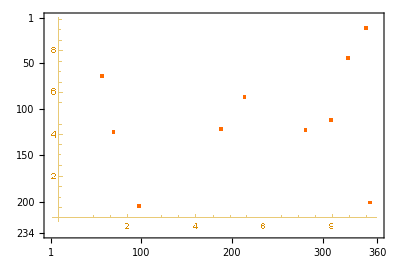

```mathematica
MatrixPlot[%344]
```

```mathematica
GetComponents[2]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
segmentation=ImageData[ImageAdd@@MapThread[ImageMultiply,{Image[{background,axes,labels,data},"Real32"],{0,1,2,3}}]]//Round
```

{{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},233}
 |  |  |  |

```mathematica
MorphologicalComponents[-Graphics-]
```

```mathematica
(*Evaluate this cell to copy the example input from a cloud object*)
```

```mathematica
ComponentMeasurements[-Graphics-,{"Image","Count","Centroid","StandardDeviation"},All,"Dataset"]
```

Dataset[<>]

```mathematica
MinMax[segmentation]
```

{0,3}

```mathematica
Colorize[segmentation]
```

-Graphics-

```mathematica
plot->segmentation
```

-Graphics-→{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},225}
 |  |  |  |

## Other ideas

```mathematica
plot=ImageRotate[Rasterize[ListPlot[Table[x^2,{x,0,10}]]],0,Background->White]
```

-Graphics-

```mathematica
ImageLines[ColorNegate[plot]]
```

```mathematica
{Line[{{0.,16.76000095879914},{360.,16.760000958799168}}],Line[{{21.979393760619676,226.},{21.22886252403712,0.}}]}
```

{Line[{{0.,16.76},{360.,16.76}}],Line[{{21.9794,226.},{21.2289,0.}}]}

```mathematica
HighlightImage[plot,%]
```

-Graphics-

```mathematica
DominantColors[plot,Automatic,{"Color","CoverageImage"},ColorCoverage->0]
```

{{RGBColor[1., 0.9999994542917262, 0.9999990613752895],-Graphics-},{RGBColor[0.3999997979338314, 0.3999994754160956, 0.39999930595934846],-Graphics-},{RGBColor[0.7019605099695899, 0.7647054401821617, 0.8627441855551392],-Graphics-},{RGBColor[0.3686265049386595, 0.505882043771485, 0.7098030258061783],-Graphics-},{RGBColor[1., 0.8117638099131591, 0.6156855836985293],-Graphics-}}

# Generating Training set

```mathematica
NetModel["Dilated ResNet-22 Trained on Cityscapes Data"]
```

General::mxcacheerr: The cached definitions of the neural networks functionality at /Users/jofre/Library/Caches/Wolfram/PacletCachedData/201904070164/MXNetLink_12.0.0_1agsyq8ky7art appear to be corrupted and will be deleted. If any neural networks functionality doesn't behave as expected, please quit the kernel and try again.

NetGraph[<>]

```mathematica
plots[n_Integer]:=Table[Rasterize[ListPlot[RandomReal[10,{10,2}],PlotRange->{{0,10},{0,10}}]],n]
```

```mathematica
plots[10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Rasterize@ListPlot[list]
```

```mathematica
rawAxes[n_]:=Table[AlphaChannel[Rasterize[ListPlot[RandomReal[10,{10,2}],PlotStyle->Transparent,LabelStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]],n]
```

```mathematica
labels=ImageDifference[Binarize[AlphaChannel[Rasterize[ListPlot[list,PlotStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]],0],
axes
]
```

-Graphics-

```mathematica
data=AlphaChannel[Rasterize[ListPlot[list,AxesStyle->Transparent,BaseStyle->{Antialiasing->False}],Background->None]]
```

-Graphics-

```mathematica
axes=ImageSubtract[rawAxes,data]
```

-Graphics-

```mathematica
background=ColorNegate[ImageAdd[axes,labels,data]]
```

-Graphics-

```mathematica
MapThread[ImageMultiply,{Image[{background,axes,labels,data},"Real32"],{0,1,2,3}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
segmentation=ImageData[ImageAdd@@MapThread[ImageMultiply,{Image[{background,axes,labels,data},"Real32"],{0,1,2,3}}]]//Round
```

```mathematica
MinMax[segmentation]
```

{0,4}

```mathematica
trainingset={1->1.9,2->4.1,3->6.0,4->8.1}
```

```mathematica
testset={3->6.0,4->8.1}
```

```mathematica
trained=NetTrain[LinearLayer[],trainingset,]
```